```mathematica
f[x_]:=(Cosh[2+Cos[x^2 √x]]/(x^2+3x+1))^(1/4)
```

```mathematica
NIntegrate[f[x], {x, 0,3}, PrecisionGoal-> 10]
```

2.93044

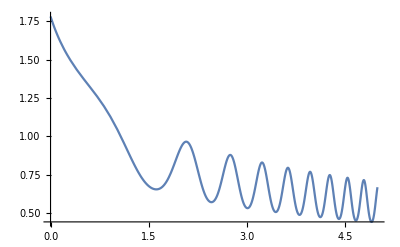

```mathematica
Plot[f[x], {x, 0,5}]
```